```mathematica
SetDirectory["/Users/jpd/Development/Osaka/SXI/E/Math"]
```

/Users/jpd/Development/Osaka/SXI/E/Math

```mathematica
<<gEDAmath.m
```

```mathematica
bipolar[options___][refdes_]:=modeleqs[refdes,i["C"]==value(v["B"]-v["E"]),i["B"]==0,i["E"]+i["C"]==0]/.{options}/.{value->gm}
```

```mathematica
current[options___][refdes_]:={i[refdes,"1"]==value}/.{options}/.value->iin
```

```mathematica
<<2v5.m
```

```mathematica
zf=Simplify[transferFunction[-stim,out]]
```

(s (r2+cfb r2 rd s+r1 (1+2 bw cfb gm π r2 rd+cfb r2 s+cfb rd s)))/(2 bw gm π r2 (1+cfb s (r1+rd+cout r1 rd s))+s (1+cout (r1+r2) s+cfb s (rd+cout r2 rd s+r1 (1+cout (r2+rd) s))))

```mathematica
zf/.s->0
```

0

To avoid typing large numbers of zeros, choose units of kiloohms, nanofarads, milliamps. These imply other units are megahertz, microseconds, millisiemens, and volts.

```mathematica
devpar={r1->2.2,r2->0.3,rd->0.001,bw->0.2,cout->47000}
```

{r1→2.2,r2→0.3,rd→0.001,bw→0.2,cout→47000}

```mathematica
zf/.devpar
```

(s (0.3+0.0003 cfb s+2.2 (1+0.000376991 cfb gm+0.301 cfb s)))/(0.376991 gm (1+cfb s (2.201+103.4 s))+s (1+117500. s+cfb s (0.001+14.1 s+2.2 (1+14147. s))))

```mathematica
natfreqs[p___]:=s/.Solve[Rationalize[Denominator[zf/.devpar/.{p}]]==0,s]
```

```mathematica
stability[z_]:=-Re[z]/Abs[z]
```

```mathematica
SetAttributes[stability,Listable]
```

```mathematica
natfreqs[gm->4000,cfb->0]
```

{-4.25532×10^-8-0.113286 ⅈ,-4.25532×10^-8+0.113286 ⅈ}

```mathematica
stability[%]
```

{3.75626×10^-7,3.75626×10^-7}

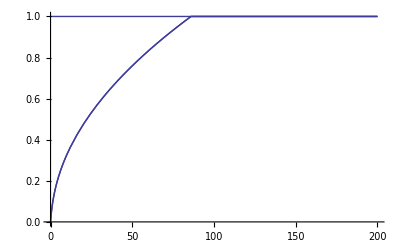

```mathematica
Plot[stability[natfreqs[gm->4000]],{cfb,0,200},PlotRange->All]
```

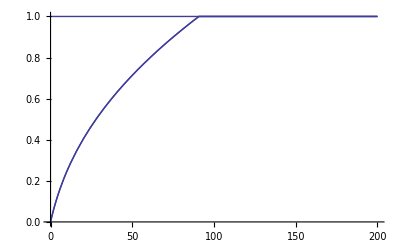

```mathematica
Plot[stability[natfreqs[gm->400]],{cfb,0,200},PlotRange->All]
```

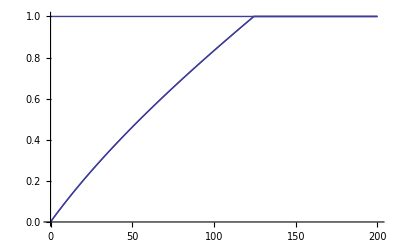

```mathematica
Plot[stability[natfreqs[gm->40]],{cfb,0,200},PlotRange->All]
```

```mathematica
natfreqs[gm->4000,cfb->100]
```

{-5.02419,-0.0145901,-0.00660668}

```mathematica
natfreqs[gm->400,cfb->1]
```

{-0.520133,-0.0134141,-0.00696718}

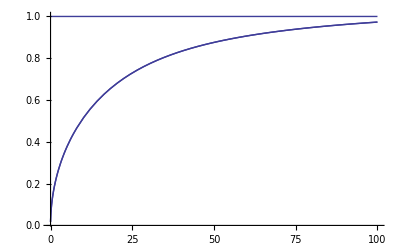

```mathematica
Plot[stability[natfreqs[cfb->1]],{gm,0,100},PlotRange->All]
```

```mathematica
optpar={gm->4000,cfb->1};
```

```mathematica
optzf=zf/.devpar/.optpar;
```

```mathematica
sr=Re[stepResponse[optzf,2500,1]];
```

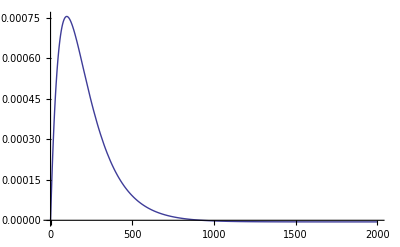

```mathematica
Plot[sr,{t,0,2000},PlotRange->All]
```